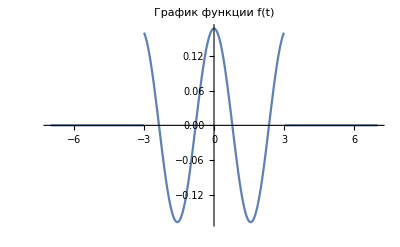

Амплитудный спектр сигнала

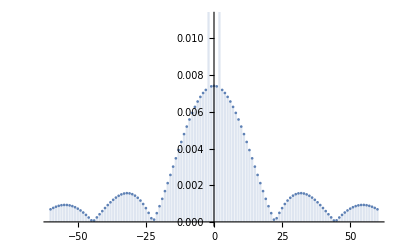

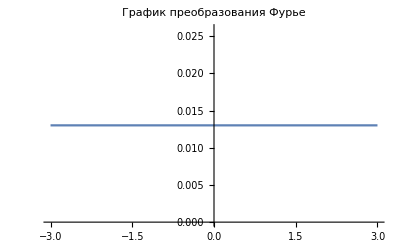

λ=3

Получение восстановленного по теореме Котельникова сигнала при N=16 и N=8

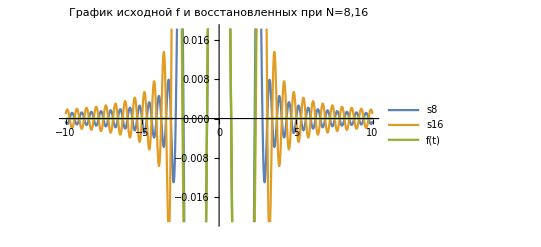

Абсолютная погрешность при N = 8:

0.172238

Абсолютная погрешность при N = 16:

0.0927514

```mathematica
Clear["Global`*"];
A=3;
l=2;
P[p_,A_]:=Which[
Abs[p]≤ A,1/(2*A),
Abs[p]> A,0];
f[p_]:=P[p,A]Cos[l*p];
Plot[f[t],{t,-7,7},PlotLabel->"График функции f(t)"]
Style[Text["Амплитудный спектр сигнала"],FontSize->18]
DiscretePlot[Abs[FourierCoefficient[f[t],t,x]],{x,-60,60}]
transform=FourierTransform[f[t],t,λ,FourierParameters->{0, -1}];
Plot[Abs[transform],{λ,-3,3},PlotLabel->"График преобразования Фурье"]
Text["λ=3"]
λ=10;
Style[Text["Получение восстановленного по теореме Котельникова сигнала при N=16 и N=8"],FontSize->18]
s8=Sum[f[k*π/λ]*Sin[λ*(t-k*π/λ)]/(λ*(t-k*π/λ)),{k,-8,8}];
s16=Sum[f[k*π/λ]*Sin[λ*(t-k*π/λ)]/(λ*(t-k*π/λ)),{k,-16,16}];
Plot[{s8,s16,f[t]},{t,-10,10},PlotLabel->"График исходной f и восстановленных при N=8,16",PlotLegends->{"s8","s16","f(t)"}]
eps8=NMaximize[Abs[f[t]-s8],t][[1]];
eps16=NMaximize[Abs[f[t]-s16],t][[1]];
Style[Text["Абсолютная погрешность при N = 8:"],FontSize->18]
eps8
Style[Text["Абсолютная погрешность при N = 16:"],FontSize->18] 
eps16
```